```mathematica
ClearAll["Global`*"];
Δ1=0.6;
Δ2=-0.6;
ϵ=0.2;
λ1=1.0;
left=(Δ2+ϵ)/(Δ2-Δ1)+10^-6;
right=(Δ2-ϵ)/(Δ2-Δ1)-10^-6;
RunSimulationHist[paramsList_,numInvocations_:Integer,xlow_:NumericQ,xhigh_:NumericQ]:=Module[{lines,inputString,output,ys,asd},lines=(StringRiffle[ToString/@Join[#,{numInvocations,N[xlow],N[xhigh]}]," "]&)/@paramsList;
inputString=StringRiffle[Prepend[lines,ToString[Length[paramsList]]],"\n"];
output=RunProcess[{"ssh", "compute2", "~/projects/kinetic/bin/pdmp_example"},"StandardOutput",inputString];
asd=StringSplit[StringTrim[output ]];
ys=Internal`StringToMReal/@asd;
ys];
Π[x_,λ_, δ_]:=x^(-2 λ (Δ2+δ ϵ)/(Δ2^2-ϵ^2)-1) ( 1-x)^(2 λ (Δ1+δ ϵ)/(Δ1^2-ϵ^2)-1) Abs[(Δ1-Δ2) x+Δ2+ϵ]^(λ (1-δ) (Δ1-Δ2)/(Δ1+ϵ)/(Δ2+ϵ)-1) Abs[(Δ1-Δ2) x+Δ2-ϵ]^(λ (1+δ) (Δ1-Δ2)/(Δ1-ϵ)/(Δ2-ϵ)-1);
```

```mathematica
Tf=15.0;
numSims = 1000;

poss = {
{0, left},
{left, right},
{right, 1}
};

getData[Δ1_,Δ2_, ϵ_, λ_, idx_] := Block[{left, right, sims, tab,f,g, Simulate2}, 
f[x_]=x*(1-x)*(Δ2+(Δ1-Δ2) x);
       g[x_]=x*(1-x)*ϵ;
Simulate2=ParametricNDSolve[{
y'[t]==f[y[t]]+ξ[t]*g[y[t]],
h'[t]==2*λ67,
WhenEvent[h[t]>=tn[t],{ξ[t]->If[RandomReal[]<=(1-δ)/2,-1,1],
h[t]->0,tn[t]->RandomVariate[ExponentialDistribution[1]]}],
tn[0]== tn0,
y[0]==y0,
h[0]==0,
ξ[0]==ξ0},
{y,h, ξ},{t,0,Tf},
{y0,ξ0,λ67,δ, tn0},(*parameters*)
DiscreteVariables->{ξ,tn}];
left=(Δ2-ϵ)/(Δ2-Δ1)+10^-4;
	right=(Δ2+ϵ)/(Δ2-Δ1)-10^-4;
sims = ParallelTable[
(y[poss[[idx]][[1]] + (poss[[idx]][[2]]-poss[[idx]][[1]])RandomReal[], RandomChoice[{-1, 1}], λ, 0 , RandomVariate[ExponentialDistribution[1]]]) /. Simulate2, 
{numSims}];
tab = Table[
{t, sims[[i]][t]}, 
{t, 0, Tf, Tf/100},
{i, 0, numSims}
];
Transpose[tab]
 ]

data1 = getData[Δ1,Δ2, ϵ, λ1, 1];
data2 = getData[Δ1, Δ2, ϵ, λ1, 2];
data3 = getData[Δ1, Δ2, ϵ, λ1, 3];
```

-Graphics-

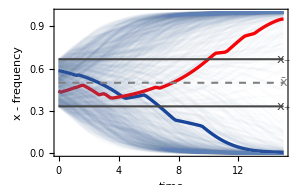

.\Documents\Bistability\BistabilityTrajectories1.svg

.\Documents\Bistability\BistabilityTrajectories2.svg

```mathematica
sz=300;

labelEpilog[Tf_,left_,right_]:={
Text[Style[Subscript["x","+"],DarkGray,13],{Tf,left},{-2.5,0}],
Text[Style[Subscript["x","-"],DarkGray,13],{Tf,right},{-2.5,0}],
Text[Style[OverBar["x"],Gray,13],{Tf,0.5},{-3.5,0}]};
firstCrossing[data_,thr_:0.55]:=SelectFirst[data,(#[[1,2]]>thr&&#[[-1,2]]<0.05)&];
firstCrossingOpposite[data_,thr_:0.45]:=SelectFirst[data,(#[[1,2]]<thr&&#[[-1,2]] >= 0.95)&];
getPlot2[data1_, data2_,l1_, l2_, ax1_, ax2_]:=Block[{},
Show[
ListLinePlot[data1,PlotStyle->Directive[ColorData[97,l1],Opacity[0.02],Thickness[0.005]],Frame->True,FrameTicks->{False,True},BaseStyle->{FontSize->14},ImageSize->sz, PlotRange->{{0, Tf}, {0, 1}}],
ListLinePlot[data2,PlotStyle->Directive[ColorData[97,l2],Opacity[0.02],Thickness[0.005]],Frame->True,FrameTicks->{False,True},BaseStyle->{FontSize->14},ImageSize->sz, PlotRange->{{0, Tf}, {0, 1}}],
ListLinePlot[{{{0,left},{Tf,left}},{{0,right},{Tf,right}},{{0,0.5},{Tf,0.5}}},PlotStyle->{Directive[DarkGray,Thickness[0.005]],Directive[DarkGray,Thickness[0.005]],Directive[Gray,Dashed,Thickness[0.005]]}],Epilog->labelEpilog[Tf,left,right],ImagePadding->{{Automatic,40},{Automatic,Automatic}},PlotRangeClipping->False,FrameLabel->{
ax1, ax2},
PlotRange->{{0, Tf}, {0, 1}}
]];
getPlot[data_,l_, ax1_, ax2_]:=Block[{},
Show[
ListLinePlot[firstCrossing[data],PlotStyle->(Directive[DarkBlue,Opacity[1.0],Thickness[0.008]] & /@ l),Frame->True,FrameTicks->{True,True},BaseStyle->{FontSize->14},ImageSize->sz, PlotRange->{{0, Tf}, {0, 1}}],
ListLinePlot[firstCrossingOpposite[data],PlotStyle->(Directive[Red,Opacity[1.0],Thickness[0.008]] & /@ l),Frame->True,FrameTicks->{True,True},BaseStyle->{FontSize->14},ImageSize->sz, PlotRange->{{0, Tf}, {0, 1}}],
ListLinePlot[data,PlotStyle->(Directive[ColorData[97,#],Opacity[0.02],Thickness[0.005]] & /@ l),Frame->True,FrameTicks->{True,True},BaseStyle->{FontSize->14},ImageSize->sz, PlotRange->{{0, Tf}, {0, 1}}],
ListLinePlot[{{{0,left},{Tf,left}},{{0,right},{Tf,right}},{{0,0.5},{Tf,0.5}}},PlotStyle->{Directive[DarkGray,Thickness[0.005]],Directive[DarkGray,Thickness[0.005]],Directive[Gray,Dashed,Thickness[0.005]]}],Epilog->labelEpilog[Tf,left,right],ImagePadding->{{Automatic,40},{Automatic,Automatic}},PlotRangeClipping->False,FrameLabel->{
ax1, ax2},
PlotRange->{{0, Tf}, {0, 1}}
]];
getPlot2[data1,data3,3, 4, None, "x - frequency"]
getPlot[data2,{1}, "time", "x - frequency"]

Export[".\\Documents\\Bistability\\BistabilityTrajectories1.svg", getPlot2[data1,data3,3, 4, None, "x - frequency"]]
Export[".\\Documents\\Bistability\\BistabilityTrajectories2.svg", getPlot[data2,{1}, "time", "x - frequency"]]
```

```mathematica
Δ1=0.6;
Δ2=-1.2;
ϵ=0.2;
λ1=1.0;
left=(Δ2+ϵ)/(Δ2-Δ1)+10^-6;
right=(Δ2-ϵ)/(Δ2-Δ1)-10^-6;
```

```mathematica
xs = Table[x, {x, left, right, (right-left)/20}];
numInvoc=10^3;
DynamicMap=ResourceFunction["DynamicMap"];
λ1=0.1;
λ2=1.0;
λ3=10.0;
getFrequency[q_, λ_] := Block[{data, freq, var},
data= RunSimulationHist[{{ Δ1,Δ2, ϵ,0, 0,λ, 0  }}, numInvoc, q, q];
freq=(Count[data, x_/;x>0.5] / numInvoc);
freq
];
datas1 =DynamicMap[{#, getFrequency[#, λ1]} & ,xs ];
datas2 =DynamicMap[{#,getFrequency[#, λ2]} & ,xs ];
datas3 =DynamicMap[{#,getFrequency[#, λ3]} & ,xs ];
```

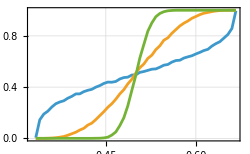

```mathematica
ListLinePlot[{datas1,datas2, datas3}, Frame->True, ImageSize->250,GridLines->Automatic, BaseStyle->{FontSize->14}]
```

```mathematica
ClearAll["Global`*"];
f[x_,Δ1_,Δ2_,ϵ_]:=x (1-x) (Δ2+(Δ1-Δ2) x);
g[x_,Δ1_,Δ2_,ϵ_]:= ϵ*x*(1-x);

left[Δ1_,Δ2_,ϵ_]:=(Δ2+ϵ)/(Δ2-Δ1)+10^-6;
right[Δ1_,Δ2_,ϵ_]:=(Δ2-ϵ)/(Δ2-Δ1)-10^-6;
H[y_,λ_,Δ1_,Δ2_,ϵ_]:=Block[{xp},xp=left[Δ1,Δ2,ϵ];(1-xp)^(-(2 Δ1 λ)/(Δ1^2-ϵ^2)) xp^((2 Δ2 λ)/(Δ2^2-ϵ^2)) (1-y)^((2 Δ1 λ)/(Δ1^2-ϵ^2)) y^(-(2 Δ2 λ)/(Δ2^2-ϵ^2)) (xp (Δ1-Δ2)+Δ2-ϵ)^(((Δ1-Δ2) λ)/((Δ1-ϵ) (-Δ2+ϵ))) (y (Δ1-Δ2)+Δ2-ϵ)^(((-Δ1+Δ2) λ)/((Δ1-ϵ) (-Δ2+ϵ))) (xp (Δ1-Δ2)+Δ2+ϵ)^(((-Δ1+Δ2) λ)/((Δ1+ϵ) (Δ2+ϵ))) (y (Δ1-Δ2)+Δ2+ϵ)^(((Δ1-Δ2) λ)/((Δ1+ϵ) (Δ2+ϵ)))];

temp[y_,λ_,Δ1_,Δ2_,ϵ_]:=H[y,λ,Δ1,Δ2,ϵ];
(*temp[y_?NumericQ,λ_,Δ1_,Δ2_,ϵ_]:=Exp[-2*λ*NIntegrate[f[t,Δ1,Δ2,ϵ]/(g[t,Δ1,Δ2,ϵ]^2-f[t,Δ1,Δ2,ϵ]^2),{t,left[Δ1,Δ2,ϵ],y}]]*)

norm[λ_,Δ1_,Δ2_,ϵ_]:=1/(1+λ*NIntegrate[1/(g[t,Δ1,Δ2,ϵ]+f[t,Δ1,Δ2,ϵ])*temp[t,λ,Δ1,Δ2,ϵ],{t,left[Δ1,Δ2,ϵ],right[Δ1,Δ2,ϵ]}]);
qplus[y_,λ_,Δ1_,Δ2_,ϵ_]:=norm[λ,Δ1,Δ2,ϵ]*(1+λ*NIntegrate[1/(g[t,Δ1,Δ2,ϵ]+f[t,Δ1,Δ2,ϵ])*temp[t,λ,Δ1,Δ2,ϵ],{t,left[Δ1,Δ2,ϵ],y}])
qminus[y_,λ_,Δ1_,Δ2_,ϵ_]:=λ*norm[λ,Δ1,Δ2,ϵ]*NIntegrate[1/(g[t,Δ1,Δ2,ϵ]-f[t,Δ1,Δ2,ϵ])*temp[t,λ,Δ1,Δ2,ϵ],{t,left[Δ1,Δ2,ϵ],y}];
hittingProb[y_,λ_,Δ1_,Δ2_,ϵ_]:=0.5*(qplus[y,λ,Δ1,Δ2,ϵ]+qminus[y,λ,Δ1,Δ2,ϵ]);

hitVal2[λ_,Δ1_,Δ2_,ϵ_]:=Block[{xs},xs=(Δ2)/(Δ2-Δ1);
hittingProb[xs, λ,Δ1,Δ2,ϵ]];

hitRelError[λ_,Δ1_,Δ2_,ϵ_]:=Abs[hitVal2[λ,Δ1,Δ2,ϵ]-0.5]/0.5;
λ=1.0;
ϵ=20.0;
```

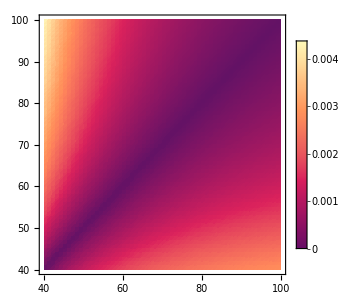

```mathematica
tab=ParallelTable[{Δ1,Δ2,hitRelError[1.0,Δ1, Δ2, ϵ]},{Δ1,40.0,100.0,1.0}, {Δ2, -100.0,-40.0, 1.0}];
ListDensityPlot[Flatten[tab,1],ColorFunctionScaling->True,PlotRange->All,PlotLegends->Automatic,ScalingFunctions->{None,"Reverse"}, BaseStyle->{FontSize->14}, ImageSize->300]
```

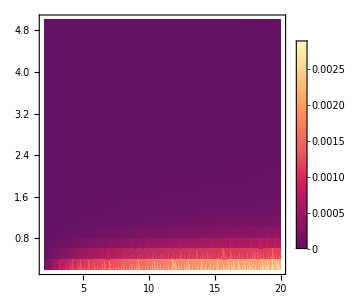

```mathematica
tab2=ParallelTable[{Δ1,λ,hitRelError[λ,Δ1, -2.0, ϵ]},{Δ1,2.0,20.0,0.2}, {λ, 0.2,5.0, 0.2}];
ListDensityPlot[Flatten[tab2,1],ColorFunctionScaling->True,PlotRange->All,PlotLegends->Automatic, BaseStyle->{FontSize->14}, ImageSize->300]
```

```mathematica
data1=ParallelTable[{x,hittingProb[x,λ1]},{x,left,right,(right-left)/50}];
data2=ParallelTable[{x,hittingProb[x,λ2]},{x,left,right,(right-left)/50}];
data3=ParallelTable[{x,hittingProb[x,λ3]},{x,left,right,(right-left)/50}];
```

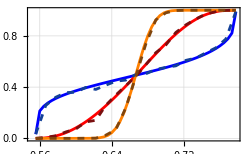

```mathematica
ListLinePlot[{data1,data2, data3, datas1, datas2, datas3}, PlotStyle->{
Directive[Blue],Directive[Red],Directive[Orange],
Directive[DarkBlue, Dashed], Directive[DarkRed, Dashed], Directive[DarkOrange, Dashed]
}, Frame->True, ImageSize->250,GridLines->Automatic, BaseStyle->{FontSize->14}]
```

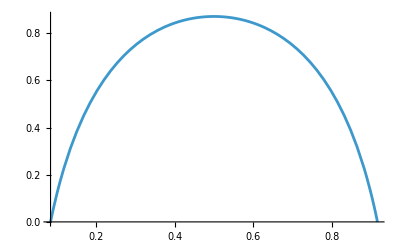

```mathematica
Plot[H[x, α,β,ϵ,λ,lp], {x, lp, lm }]
```